```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["ErrorBarPlots`"];
```

## Debye mass HTL Fitting

### Analytic Expression

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1]; 

mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
mDcalT[μ_,T_,c_,d_]:=1/T mDcal[μ,T,c,d];
```

NDSolve::precw: The precision of the differential equation ({{as'[t]==1/12 as[t]^2 (-33.+2 If[«3»])+1/96 as[t]^3 (-612.+76. If[«3»])+1/128 as[t]^4 (-2857+5033/9 If[«3»]-325/27 Power[«2»])+1/256 as[t]^5 (-149753/6-1093/729 Power[«2»]-3564 Zeta[«1»]-Power[«2»] Plus[«2»]+If[«3»] Plus[«2»]),as[10000 Log[4]]==0.0000376185},{},{},{},{}}) is less than WorkingPrecision (32.).

NDSolve::ndsz: At t == 2.05914, step size is effectively zero; singularity or stiff system suspected.

### Fitting

```mathematica
β={6.8,6.9,7,7.125,7.25,7.3,7.48};
T={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
Tclatt=0.1725;
Tccont={0.155,9};
```

```mathematica
md={{0.038919565918040445,0.06743682653727344},{0.12582094383686163,0.10923208048614581},{0.1892583277055926,0.12852782269560006},{0.30988003094936495,0.18358091276753688},{0.48025965960625705,0.1479696311077649},{0.49657169002278573,0.1791783591997105},{0.6465066249674667,0.1798587912586749}};
σmd={0.2088095376752115,0.21706712111822724,0.22532470456124298,0.23564668386501264,0.2459686631687824,0.2500974548902902,0.26496110508771864};
σmderr={0.01621039222655274,0.015928132568206136,0.015645872909859533,0.015293048336926279,0.014940223763993024,0.014799093934819724,0.014291026549795836};
```

```mathematica
σc={0.20995290463247063,0.21149352214966277,0.2130133803006149,0.21451314748978678,0.2159934921216372,0.21745508260062596,0.21889858733121204,0.220324674717855,0.22173401316501407,0.22312727107714847,0.22450511685871766,0.22587126046856376,0.22722793659031448,0.22857049076380875,0.2298986163511385,0.231212006714396,0.23251035521567331,0.23379335521706246,0.2350607000806556,0.23629993449898445,0.23751285961191504,0.23871164696063274,0.23989796608612768,0.2410734865293893,0.2422398778314072,0.24339880953317128,0.2445519511756712,0.2457009722998964,0.24685667552572566,0.24800837746923,0.24915173528845158,0.2502857723441001,0.251409511996885,0.25252197760751594};
σcerr={0.016171309803838168,0.016118648613424984,0.01606669701700655,0.016015432167267356,0.015964831216891885,0.015914871318564616,0.015865529624970037,0.015816783288792633,0.015768609462716878,0.01572098529942727,0.015673887951608283,0.015627190605922516,0.015580816876700775,0.015534925862103421,0.015489528043588108,0.01544463390261248,0.01540025392063418,0.015356398579110857,0.015313078359500156,0.015270719007524764,0.015229258956852756,0.015188282161424121,0.015147731553202846,0.01510755006415291,0.0150676806262383,0.015028066171422994,0.014988649631670972,0.014949373938946225,0.014909869839481324,0.014870502511335752,0.01483142040097641,0.014792656891762287,0.01475424536705237,0.014716219210205647};
σb={0.20995290463247063,0.2125090262536785,0.21500872075470046,0.21745508260062596,0.2198512062565443,0.2222001861875451,0.22450511685871766,0.22677726517914676,0.2290148176117719,0.231212006714396,0.23336741286707507,0.23547961644986515,0.23751285961191504,0.2395038086776795,0.2414632155326204,0.24339880953317128,0.24531832003576604,0.24724144301210482,0.24915173528845158,0.251036136554873,0.2528901253331727,0.2547091801451543,0.2564887795126215,0.25822440195737806,0.25991152600122747,0.26154563016597343,0.26312219297341966,0.26463669294536996,0.26629065177969047,0.26799519882068,0.26969974586166945,0.2714042929026589,0.27310883994364843,0.274813386984638,0.2765179340256274,0.27822248106661696,0.2799270281076064,0.28163157514859594,0.28333612218958537,0.2850406692305749,0.28674521627156446,0.2884497633125539,0.29015431035354333,0.2918588573945329,0.2935634044355224,0.29526795147651186,0.2969724985175014,0.29867704555849095,0.3003815925994804,0.3020861396404698,0.30379068668145937,0.3054952337224488,0.30719978076343835,0.3089043278044279,0.31060887484541744,0.3123134218864069,0.3140179689273963,0.31572251596838585,0.3174270630093753,0.31913161005036483,0.32083615709135427,0.3225407041323439,0.32424525117333336,0.3259497982143228,0.32765434525531234,0.3293588922963018,0.3310634393372913,0.33276798637828076,0.3344725334192704,0.33617708046025985,0.3378816275012493,0.33958617454223883,0.34129072158322826,0.3429952686242178,0.34469981566520724,0.3464043627061969,0.34810890974718633,0.34981345678817577,0.3515180038291653,0.35322255087015475,0.3549270979111443,0.35663164495213373,0.3583361919931234,0.3600407390341127,0.36174528607510226,0.3634498331160918,0.36515438015708124,0.3668589271980708,0.3685634742390602,0.37026802128004965,0.3719725683210392};
σberr={0.016171309803838168,0.01608393678236362,0.015998492545475394,0.015914871318564616,0.015832967327022423,0.015752674796239933,0.015673887951608283,0.015596221669085936,0.015519737938764135,0.01544463390261248,0.015370958085897852,0.015298759013887137,0.015229258956852756,0.01516120459119406,0.015094228397340956,0.015028066171422994,0.01496245370956972,0.014896717766602167,0.01483142040097641,0.014767008038531815,0.014703635231856284,0.014641456533537715,0.014580626496164012,0.014521299672323074,0.014463630614602794,0.014407773875591081,0.014353884007875836,0.01430211556404495,0.014245580155263886,0.014187315546889585,0.014129050938515287,0.014070786330140986,0.014012521721766685,0.013954257113392387,0.01389599250501809,0.013837727896643792,0.013779463288269494,0.013721198679895193,0.013662934071520895,0.013604669463146594,0.013546404854772296,0.013488140246397995,0.013429875638023697,0.0133716110296494,0.013313346421275098,0.0132550818129008,0.013196817204526503,0.013138552596152202,0.013080287987777904,0.013022023379403603,0.012963758771029305,0.012905494162655008,0.012847229554280706,0.012788964945906405,0.012730700337532107,0.01267243572915781,0.012614171120783512,0.012555906512409214,0.012497641904034913,0.012439377295660616,0.012381112687286318,0.012322848078912013,0.012264583470537715,0.012206318862163418,0.01214805425378912,0.012089789645414822,0.012031525037040525,0.011973260428666224,0.011914995820291922,0.011856731211917625,0.011798466603543323,0.011740201995169026,0.011681937386794728,0.01162367277842043,0.011565408170046133,0.011507143561671828,0.01144887895329753,0.011390614344923233,0.011332349736548935,0.011274085128174634,0.011215820519800336,0.011157555911426038,0.011099291303051734,0.011041026694677443,0.010982762086303138,0.01092449747792884,0.010866232869554543,0.010807968261180242,0.010749703652805944,0.010691439044431646,0.010633174436057349};
```

```mathematica
αcont={0.5138562580709736,0.0027118637679895965};
σcont={0.16949622818854412,0.0009172672238755708};
ccont={-0.15942304870711493,0.0023023051670536016};
```

```mathematica
Table[md[[n,1]]/√σmd[[n]],{n,1,Length[T]}]
```

{0.0851712,0.270057,0.398704,0.638356,0.968359,0.99295,1.25598}

```mathematica
Table[md[[n,1]]/T[[n]],{n,1,Length[T]}]
```

{0.263326,0.766266,1.04102,1.50867,2.07277,2.04772,2.25972}

```mathematica
mDfit=NonlinearModelFit[Table[{T[[n]](155/172.5),md[[n,1]]/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x];
{k1,k2}={d,e}/.mDfit["BestFitParameters"];
mDfit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.503185 | 0.0966623 | 5.2056 | 0.00345094
e | -0.270021 | 0.0394174 | -6.85029 | 0.00101247

```mathematica
mDfitupper=NonlinearModelFit[Table[{T[[n]](155/172.5),(md[[n,1]]+md[[n,2]])/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x];
{k1u,k2u}={d,e}/.mDfitupper["BestFitParameters"];
mDfitupper["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.877254 | 0.0664694 | 13.1979 | 0.0000446105
e | -0.383222 | 0.0271052 | -14.1383 | 0.0000318649

```mathematica
mDfitlower=NonlinearModelFit[Table[{T[[n]](155/172.5),(md[[n,1]]-md[[n,2]])/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x];
{k1l,k2l}={d,e}/.mDfitlower["BestFitParameters"];
mDfitlower["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.129116 | 0.153394 | 0.841727 | 0.438334
e | -0.156819 | 0.0625515 | -2.50704 | 0.0540234

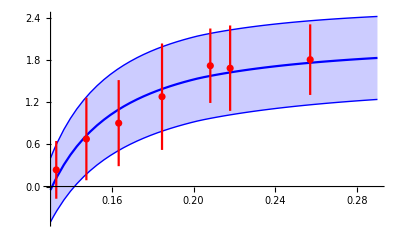

```mathematica
Show[{Plot[{mDcalT[2π,x,k1,k2],mDcalT[2π,x,k1u,k2u],mDcalT[2π,x,k1l,k2l]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{T[[n]](155/172.5),md[[n,1]]/T[[n]] √(σcont[[1]]/σmd[[n]]),md[[n,2]]/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

```mathematica
mdrandu[n_]:=Module[{m},m=md[[n,1]]+Abs[RandomVariate[NormalDistribution[0,md[[n,2]]]]];If[m>0,m,0]]
mdrandl[n_]:=Module[{m},m=md[[n,1]]-Abs[RandomVariate[NormalDistribution[0,md[[n,2]]]]];If[m>0,m,0]]
σrand[n_]:=RandomVariate[NormalDistribution[σmd[[n]],σmderr[[n]]]];
σcontrand:=RandomVariate[NormalDistribution[σcont[[1]],σcont[[2]]]];
```

```mathematica
fitsu={{},{}};
fitsl={{},{}};
SetSharedVariable[fitsu,fitsl];
Module[{k1u,k2u,k1l,k2l},ParallelDo[Quiet[{k1u,k2u}={d,e}/.NonlinearModelFit[Table[{T[[n]](155/172.5),mdrandu[n]/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x]["BestFitParameters"];
{k1l,k2l}={d,e}/.NonlinearModelFit[Table[{T[[n]](155/172.5),mdrandl[n]/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x]["BestFitParameters"]];
fitsu[[1]]=Append[fitsu[[1]],k1u];
fitsu[[2]]=Append[fitsu[[2]],k2u];
fitsl[[1]]=Append[fitsl[[1]],k1l];fitsl[[2]]=Append[fitsl[[2]],k2l],{i,1,100000}]]
```

```mathematica
kfinalu={Mean[fitsu[[1]]],Mean[fitsu[[2]]]}
kfinall={Mean[fitsl[[1]]],Mean[fitsl[[2]]]}
```

{0.801696,-0.360406}

{0.13899,-0.149229}

```mathematica
kfinalu={0.8016955527941704,-0.36040626803845205};
kfinall={0.1389898610341079,-0.14922900812090412};
```

```mathematica
kfinal={Mean[{kfinalu[[1]],kfinall[[1]]}],Mean[{kfinalu[[2]],kfinall[[2]]}]}
```

{0.470343,-0.254818}

```mathematica
kfinal={0.47034270691413915,-0.25481763807967805}(*100k run*)
```

{0.470343,-0.254818}

```mathematica
kerror={kfinalu[[1]]-kfinal[[1]],kfinal[[2]]-kfinalu[[2]]}
```

{0.331353,0.105589}

```mathematica
kerror={0.3313528458800312,0.105588629958774};
```

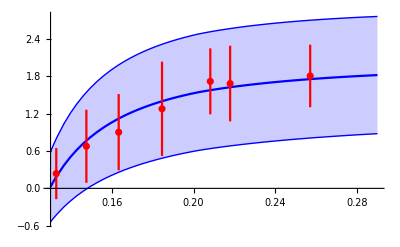

```mathematica
Show[{Plot[{mDcalT[2π,x,kfinal[[1]],kfinal[[2]]],mDcalT[2π,x,kfinal[[1]]+1.96 kerror[[1]],kfinal[[2]]-1.96 kerror[[2]]],mDcalT[2π,x,kfinal[[1]]-1.96 kerror[[1]],kfinal[[2]]+1.96 kerror[[2]]]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{T[[n]](155/172.5),md[[n,1]]/T[[n]] √(σcont[[1]]/σmd[[n]]),md[[n,2]]/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

## Generate Spectral Functions

```mathematica
R=20000;
Mc=1.4689783072176936;
Mb=4.882;
```

### Define required functions

```mathematica
g[x_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p x],{p,0,∞}]];
ϕ[x_]:=Quiet[2NIntegrate[z/((z^2+1)^2)Sinc[x z],{z,0,∞}]];
ReV[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c
```

```mathematica
Clear[ParabolicCylinderI,ParabolicCylinderR];
ParabolicCylinderI[r_]=If[r<20,ParabolicCylinderD[-1/2,ⅈ √2 r],ⅇ^(r^2/2) (((1-ⅈ) √(1/r))/2^(3/4)+((3/16-(3 ⅈ)/16) (1/r)^(5/2))/2^(3/4)+((105/512-(105 ⅈ)/512) (1/r)^(9/2))/2^(3/4)+((3465/8192-(3465 ⅈ)/8192) (1/r)^(13/2))/2^(3/4)+((675675/524288-(675675 ⅈ)/524288) (1/r)^(17/2))/2^(3/4))];
ParabolicCylinderR[r_]=ParabolicCylinderD[-1/2,√2 r];
```

```mathematica
ϵ=1/1000;ϕ1table=Quiet[ Join[Parallelize[Table[{x,1-ϕ[x]},{x,ϵ/100,2,10ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,2+100ϵ,10,100ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,10+1000ϵ,100,10000ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,100+100000ϵ,10000,100000ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,10000+10000000ϵ,1000000,10000000ϵ}]]]];
```

```mathematica
TableT[σ1_,α1_, mD1_]:=Module[{σ=σ1, α=α1,mD=mD1,r,μ,c1},
μ=(mD^2 σ/α)^(1/4);
r=mD/μ;
pg=1;
c1=Re[ParabolicCylinderI[ϵ/100]NIntegrate[ParabolicCylinderR[x] x^2 g[x r],{x,0,∞},PrecisionGoal->pg]];
ψ1[x_,r_]:=c1-ParabolicCylinderR[x]NIntegrate[y^2 g[y r]Re[ParabolicCylinderI[y]],{y,0,x},PrecisionGoal->pg]-Re[ParabolicCylinderI[x]]NIntegrate[ParabolicCylinderR[y] y^2 g[y r],{y,x,∞},PrecisionGoal->pg];
ψ1table=Join[Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,ϵ/100,1,10ϵ}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,1+100ϵ,10+ϵ,100ϵ}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,11,100,1}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,200,1000,100}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,2000,20000,1000}]]];];
```

### Modules

```mathematica
swaveccspectra[n_,Tscan_]:=Module[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ρtable,ccsT,Tstring},
TableT[σ,α,mD];

rev=Interpolation[Join[Table[{r,ReV[r,mD,α,σ,c]},{r,0.001,10,0.01}],Table[{r,ReV[r,mD,α,σ,c]},{r,10.1,25,0.1}],Table[{r,ReV[r,mD,α,σ,c]},{r,26,1000,1}],Table[{r,ReV[r,mD,α,σ,c]},{r,1010,20000,10}]]];
ϕ1=Interpolation[ϕ1table,InterpolationOrder->1];
ψ1inter=Interpolation[ψ1table,InterpolationOrder->1];
V[x_]:=rev[x]+ⅈ (α T ϕ1[mD x]+α T ψ1inter[(mD^2 σ/α)^(1/4) x]);

δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=2;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω M}];
SetSharedVariable[ρtable];

ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2M,rhow[inf]},{it,1,Length[ρtable]}];

ccsT=Table[{ρtable[[i]][[1]],(-ρtable[[i]][[2]])/(ρtable[[i]][[1]])^2},{i,1,Length[ρtable]}];
Tstring=IntegerPart[T*1000];
Export["spectraldata/Tscan/cc/swccT"<>ToString[Tstring]<>"lspectra.dat",ccsT]
]
```

```mathematica
swavebbspectra[n_,Tscan_]:=Module[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,Tstring,ρtable,bbsT},
TableT[σ,α,mD];

rev=Interpolation[Join[Table[{r,ReV[r,mD,α,σ,c]},{r,0.001,10,0.01}],Table[{r,ReV[r,mD,α,σ,c]},{r,10.1,25,0.1}],Table[{r,ReV[r,mD,α,σ,c]},{r,26,1000,1}],Table[{r,ReV[r,mD,α,σ,c]},{r,1010,20000,10}]]];
ϕ1=Interpolation[ϕ1table,InterpolationOrder->1];
ψ1inter=Interpolation[ψ1table,InterpolationOrder->1];
V[x_]:=rev[x]+ⅈ (α T ϕ1[mD x]+α T ψ1inter[(mD^2 σ/α)^(1/4) x]);

δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=3;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω M}];
SetSharedVariable[ρtable];
ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2M,rhow[inf]},{it,1,Length[ρtable]}];

bbsT=Table[{ρtable[[i]][[1]],(-ρtable[[i]][[2]])/(ρtable[[i]][[1]])^2},{i,1,Length[ρtable]}];

Tstring=IntegerPart[T*1000]
Export["spectraldata/Tscan/bb/swbbT"<>ToString[Tstring]<>"spectra.dat",bbsT]
]
```

### Run modules

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
Tscancorig=Table[i,{i,0.15,0.25,0.003}];
Tscanc=Table[i,{i,0.174,0.25,0.003}];
Do[swaveccspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

NIntegrate::inumr: The integrand (p Sinc[0.334986 p x])/(1+p^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{23701.9,Null}

```mathematica
Tscanborig=Table[i,{i,0.15,0.6,0.005}];
Tscanb={0.15};
Do[swavebbspectra[i,Tscanb],{i,Length[Tscanb]}]//AbsoluteTiming
```